```mathematica
ClearAll["Global`*"]
```

```mathematica
FullSimplify[DSolve[{x'[l]==b/a(L/l -1), x[1] == x0},x[l],l]]
```

{{x[l]→(b-b l+a x0+b L Log[l])/a}}

```mathematica
FullSimplify[Solve[b/a(1- l+ L Log[l])== 0, l]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→-L ProductLog[-ⅇ^(-1/L)/L]}}

```mathematica
FullSimplify[Solve[b/a(1- l+ L Log[l]) +x0 == 0, l]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→-L ProductLog[-ⅇ^(-(b+a x0)/(b L))/L]}}

```mathematica
DSolve[{l'[t]== l[t](C+D-C l[t]+C L Log[l[t]]), l[0] == x0},l[t],t]
```

{{l[t]→InverseFunction[∫_1^#1 1/(K[1] (-C-D+C K[1]-C L Log[K[1]]))ⅆK[1]&][-t+∫_1^x0 1/(K[1] (-C-D+C K[1]-C L Log[K[1]]))ⅆK[1]]}}

```mathematica
Solve[Eliminate[{x==FullSimplify[Integrate[1, {l,1, y }]/ Integrate[1/ l, {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]
```

{{x→L}}

```mathematica
FullSimplify[Solve[Eliminate[{x==FullSimplify[Integrate[l, {l,1, y }]/ Integrate[1/ l, {l,1, y }]-L^2 ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1/2 L (-1+2 L+L ProductLog[-ⅇ^(-1/L)/L])}}

```mathematica
FullSimplify[Solve[Eliminate[{x==FullSimplify[Integrate[1/ l, {l,1, y }]/Integrate[b( 1-l+L Log[l])/(l a), {l,1, y }] ,Re[y]>0],1- y+ L Log[y]==0}, y] , x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(2 a)/(b-2 b L-b L ProductLog[-ⅇ^(-1/L)/L])}}

```mathematica
Manipulate[GraphicsRow[{Plot[{b( 1-l+L Log[l])/a , b/a(1- L+ L Log[L])},{l,0,1},GridLines->{{-L ProductLog[-ⅇ^(-1/L)/L],L},None}, PlotRange->{{0,1},{0,1}}],Module[{sol},sol=NDSolve[{x'[t]==b (l[t]-L) x[t],l'[t]==-a l[t] x[t],g'[t]==b g[t](g[t]-1- L Log[g[t]]) -a g[t]x0,x[0]==x0,l[0]==1, g[0]==1},{x,l, g},{t,0,15}];Plot[Evaluate[{x[t],b/a(1- L+ L Log[L]),l[t]}/.sol],{t,0,15},PlotRange->Full,GridLines->{None,{-L ProductLog[-ⅇ^(-1/L)/L],L}}]]}],{{b,4},0,10},{{a,1},0,10},{{L,0.5},0,1},{{x0,0.0001},0,0.001},Paneled->False]
```

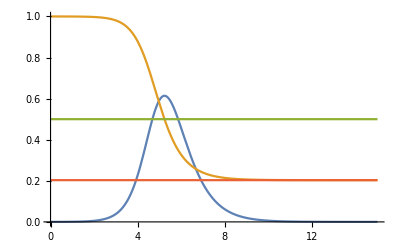

```mathematica
Module[{sol},sol=NDSolve[{x'[t]==4 (l[t]-0.5) x[t],l'[t]==- l[t] x[t],g'[t]==4 g[t](g[t]-1- 0.5 Log[g[t]]) -1 g[t]0.0001,x[0]==0.0001,l[0]==1, g[0]==1},{x,l, g},{t,0,15}];Plot[Evaluate[{x[t],l[t],0.5,-0.5 ProductLog[-ⅇ^(-1/0.5)/0.5]}/.sol],{t,0,15},PlotRange->Full]]
```

```mathematica
Export["disks.svg",%]
```

disks.svg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["disks.svg"]]]
```

```mathematica
F[x]= x^k/(x^k + a^k)
```

x^k/(a^k+x^k)

```mathematica
FullSimplify[D[F[x], x]/ (2F[x])]
```

(a^k k)/(2 a^k x+2 x^(1+k))

```mathematica
Solve[FullSimplify[D[F[x], x]/ (2F[x])] (1-x) ==c , x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(a^k k (1-x))/(2 a^k x+2 x^(1+k))==c,x]

```mathematica
G[x]= x^k
```

x^k

```mathematica
Solve[FullSimplify[D[G[x], x]/ (2G[x])] (1-x) ==c /d, x]
```

{{x→(d k)/(2 c+d k)}}